NY VEI TO DO DAT FRA 20180515 YERNAL

```mathematica
Options[loadKappaCSV]={subtract1point5->True,earlyMLTStr->"20_50-23MLT",lateMLTStr->"23-1_50MLT",allMLTStr->"20_50-1_50MLT",printFName->False};
loadKappaCSV[EarlyOrLate_,BeamNoBeam_,Dst_,GoverK_,ventileOrDecile_,dateStr_,OptionsPattern[]]:=Module[{earlyNames,lateNames,allNames,dstStr,GoverKStr},
If[OptionValue[subtract1point5],subVal=1.5,subVal=0];
GoverKStr=(Switch[ToUpperCase[ventileOrDecile],"VENTILE","Ven","DECILE","Dec"])<>ToString[GoverK];
dstStr=If[Dst==0,"","-Dst"<>ToString[Dst]];
inDir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/txtOutput/";
earlyNames={dateStr<>OptionValue[earlyMLTStr]<>"-ionBeam-data-allALT"<>dstStr<>"-BOTH-GK"<>GoverKStr<>"-Kchi2Max5_0-combo.csv",
dateStr<>OptionValue[earlyMLTStr]<>"-noBeam-data-allALT"<>dstStr<>"-BOTH-GK"<>GoverKStr<>"-Kchi2Max5_0-combo.csv"};
lateNames={dateStr<>OptionValue[lateMLTStr]<>"-ionBeam-data-allALT"<>dstStr<>"-BOTH-GK"<>GoverKStr<>"-Kchi2Max5_0-combo.csv",
dateStr<>OptionValue[lateMLTStr]<>"-noBeam-data-allALT"<>dstStr<>"-BOTH-GK"<>GoverKStr<>"-Kchi2Max5_0-combo.csv"};
allNames={dateStr<>OptionValue[allMLTStr]<>"-ionBeam-data-allALT"<>dstStr<>"-BOTH-GK"<>GoverKStr<>"-Kchi2Max5_0-combo.csv",
dateStr<>OptionValue[allMLTStr]<>"-noBeam-data-allALT"<>dstStr<>"-BOTH-GK"<>GoverKStr<>"-Kchi2Max5_0-combo.csv"};
Switch[ToUpperCase[EarlyOrLate],
"EARLY",
names=earlyNames;,
"LATE",
names=lateNames;,
"ALL",
names=allNames;
];
Switch[BeamNoBeam//ToUpperCase,
"BEAM",
fName=names[[1]];,
"NOBEAM",
fName=names[[2]];
];
If[OptionValue[printFName],Print[fName]];
data=Import[inDir<>fName]//Flatten;
data=data-subVal
]
```

ALD VEI TO DO DAT

```mathematica
(*Options[loadKappaCSV]={subtract1point5->True,earlyMLTStr->"20_50-23MLT",lateMLTStr->"23-1_50MLT",printFName->False};
loadKappaCSV[EarlyOrLate_,BeamNoBeam_,Dst_,GoverK_,ventileOrDecile_,dateStr_,OptionsPattern[]]:=Module[{earlyNames,lateNames,allNames,dstStr,GoverKStr},
If[OptionValue[subtract1point5],subVal=1.5,subVal=0];
GoverKStr=(Switch[ToUpperCase[ventileOrDecile],"VENTILE","Ven","DECILE","Dec"])<>ToString[GoverK];
dstStr=If[Dst==0,"","-Dst"<>ToString[Dst]];
inDir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/txtOutput/";
earlyNames={dateStr<>OptionValue[earlyMLTStr]<>"-ionBeam-data-allALT"<>dstStr<>"-BOTH-GK"<>GoverKStr<>"-Kchi2Max5_0-combo.csv",
dateStr<>OptionValue[earlyMLTStr]<>"-noBeam-data-allALT"<>dstStr<>"-BOTH-GK"<>GoverKStr<>"-Kchi2Max5_0-combo.csv"};
lateNames={dateStr<>OptionValue[lateMLTStr]<>"-ionBeam-data-allALT"<>dstStr<>"-BOTH-GK"<>GoverKStr<>"-Kchi2Max5_0-combo.csv",
dateStr<>OptionValue[lateMLTStr]<>"-noBeam-data-allALT"<>dstStr<>"-BOTH-GK"<>GoverKStr<>"-Kchi2Max5_0-combo.csv"};
allNames={dateStr<>"20_50-1_50MLT-ionBeam-data-allALT"<>dstStr<>"-BOTH-GK"<>GoverKStr<>"-Kchi2Max5_0-combo.csv",
dateStr<>"20_50-1_50MLT-noBeam-data-allALT"<>dstStr<>"-BOTH-GK"<>GoverKStr<>"-Kchi2Max5_0-combo.csv"};
Switch[ToUpperCase[EarlyOrLate],
"EARLY",
names=earlyNames;,
"LATE",
names=lateNames;,
"ALL",
names=allNames;
];
Switch[BeamNoBeam//ToUpperCase,
"BEAM",
fName=names[[1]];,
"NOBEAM",
fName=names[[2]];
];
If[OptionValue[printFName],Print[fName]];
data=Import[inDir<>fName]//Flatten;
data=data-subVal
]*)
```

Essaye avec 20.5–23 MLT and 23–1.5 MLT divisions

```mathematica
earlyMLTStr="20_50-23MLT";
lateMLTStr="23-1_50MLT";
```

```mathematica
dateStr="20180514-";
```

```mathematica
statType="ventile";
tile=5;
dstCutoff=-20;
```

```mathematica
EBData=loadKappaCSV["Early","Beam",dstCutoff,tile,statType,dateStr];
ENData=loadKappaCSV["Early","NoBeam",dstCutoff,tile,statType,dateStr];
LBData=loadKappaCSV["Late","Beam",dstCutoff,tile,statType,dateStr];
LNData=loadKappaCSV["Late","NoBeam",dstCutoff,tile,statType,dateStr];
```

```mathematica
EBDist=SmoothKernelDistribution[EBData];
ENDist=SmoothKernelDistribution[ENData];
LBDist=SmoothKernelDistribution[LBData];
LNDist=SmoothKernelDistribution[LNData];
```

```mathematica
plotMin=0;plotMax=20;
```

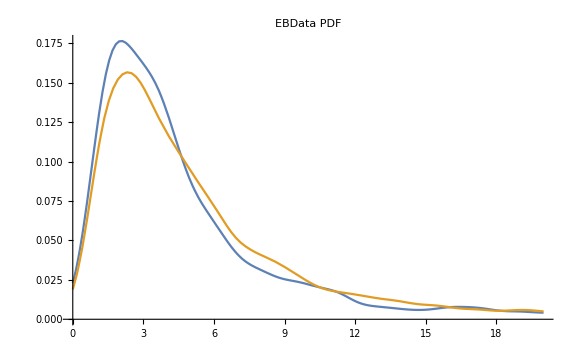
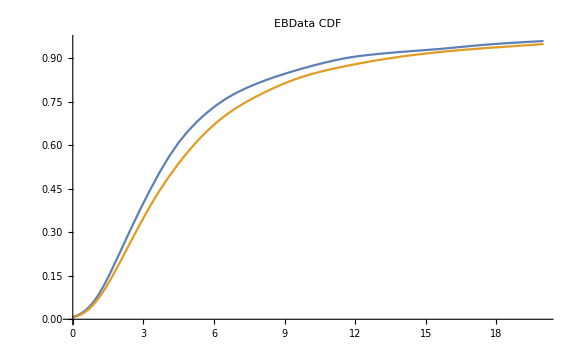

```mathematica
Table[Plot[{Evaluate[f[EBDist,x]],Evaluate[f[ENDist,x]]},{x,plotMin,plotMax},PlotLabel->("EBData "<>ToString[f]),ImageSize->Large],{f,{PDF,CDF}}]
```

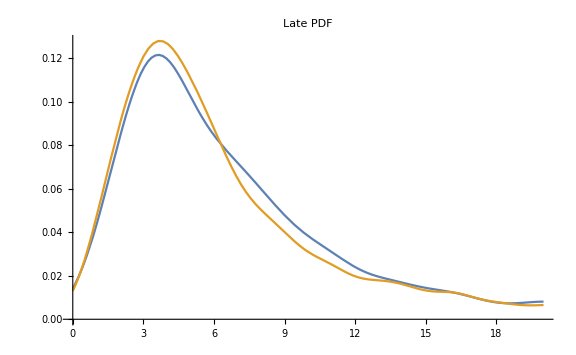
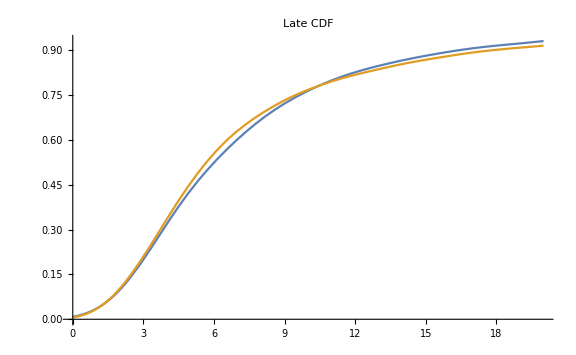

```mathematica
Table[Plot[{Evaluate[f[LBDist,x]],Evaluate[f[LNDist,x]]},{x,plotMin,plotMax},PlotLabel->("Late "<>ToString[f]),ImageSize->Large],{f,{PDF,CDF}}]
```

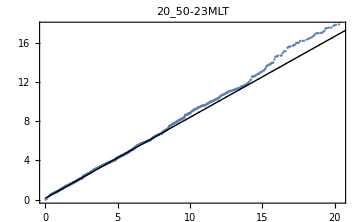
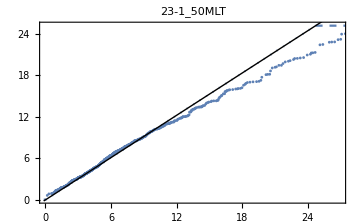

```mathematica
Table[QuantilePlot[dataz[[1]],dataz[[2]],PlotLabel->dataz[[3]],ImageSize->Medium],{dataz,{{EBData,ENData,earlyMLTStr},{LBData,LNData,lateMLTStr}}}]
```

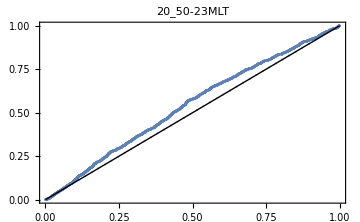
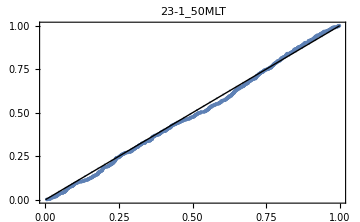

```mathematica
Table[ProbabilityPlot[dataz[[1]],dataz[[2]],PlotLabel->dataz[[3]],ImageSize->Medium],{dataz,{{EBData,ENData,earlyMLTStr},{LBData,LNData,lateMLTStr}}}]
```

Essaye avec 20.5–22.25 MLT and 22.25–1.5 MLT divisions

```mathematica
earlyMLTStr="20_50-22_25MLT";
lateMLTStr="22_25-1_50MLT";
```

```mathematica
dateStr="20180515-";
```

```mathematica
statType="ventile";
tile=5;
dstCutoff=-20;
```

```mathematica
EBData=loadKappaCSV["Early","Beam",dstCutoff,tile,statType,dateStr,earlyMLTStr->earlyMLTStr,lateMLTStr->lateMLTStr];
ENData=loadKappaCSV["Early","NoBeam",dstCutoff,tile,statType,dateStr,earlyMLTStr->earlyMLTStr,lateMLTStr->lateMLTStr];
LBData=loadKappaCSV["Late","Beam",dstCutoff,tile,statType,dateStr,earlyMLTStr->earlyMLTStr,lateMLTStr->lateMLTStr];
LNData=loadKappaCSV["Late","NoBeam",dstCutoff,tile,statType,dateStr,earlyMLTStr->earlyMLTStr,lateMLTStr->lateMLTStr];
ABData=loadKappaCSV["All","Beam",dstCutoff,tile,statType,dateStr,earlyMLTStr->earlyMLTStr,lateMLTStr->lateMLTStr,printFName->True];
ANData=loadKappaCSV["All","NoBeam",dstCutoff,tile,statType,dateStr,earlyMLTStr->earlyMLTStr,lateMLTStr->lateMLTStr];
```

20180515-20_50-1_50MLT-ionBeam-data-allALT-Dst-20-BOTH-GKVen5-Kchi2Max5_0-combo.csv

```mathematica
EBDist=SmoothKernelDistribution[EBData];
ENDist=SmoothKernelDistribution[ENData];
LBDist=SmoothKernelDistribution[LBData];
LNDist=SmoothKernelDistribution[LNData];
ABDist=SmoothKernelDistribution[ABData];
ANDist=SmoothKernelDistribution[ANData];
```

```mathematica
plotMin=0;plotMax=20;
```

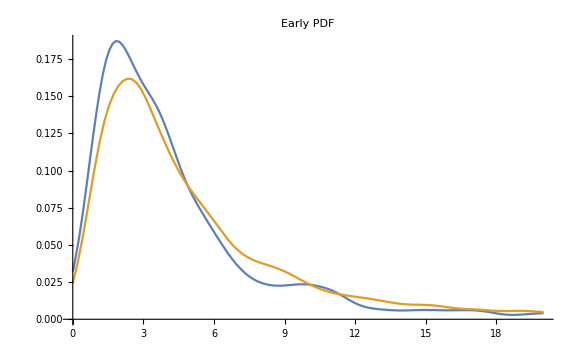
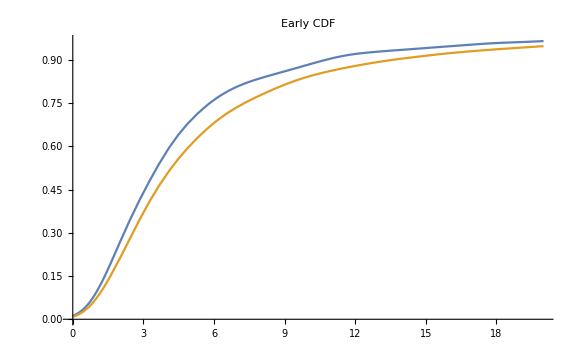

```mathematica
Table[Plot[{Evaluate[f[EBDist,x]],Evaluate[f[ENDist,x]]},{x,plotMin,plotMax},PlotLabel->("Early "<>ToString[f]),ImageSize->Large],{f,{PDF,CDF}}]
```

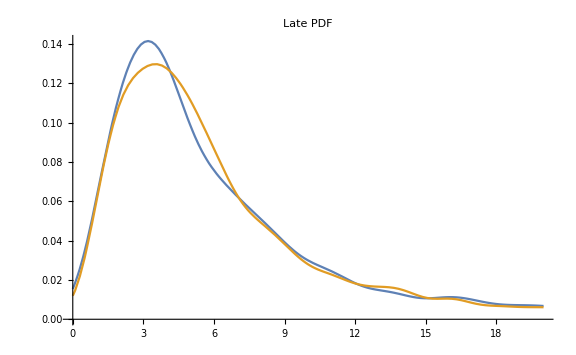
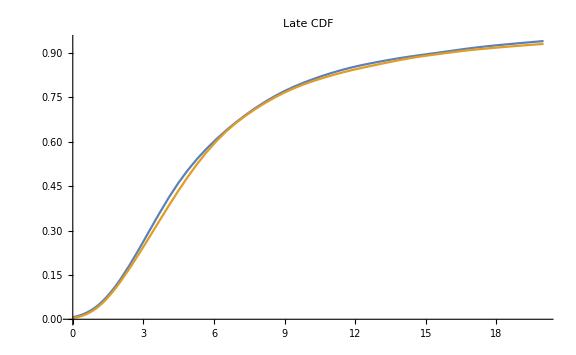

```mathematica
Table[Plot[{Evaluate[f[LBDist,x]],Evaluate[f[LNDist,x]]},{x,plotMin,plotMax},PlotLabel->("Late "<>ToString[f]),ImageSize->Large],{f,{PDF,CDF}}]
```

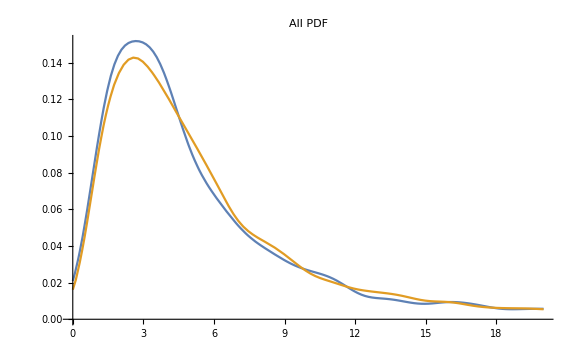
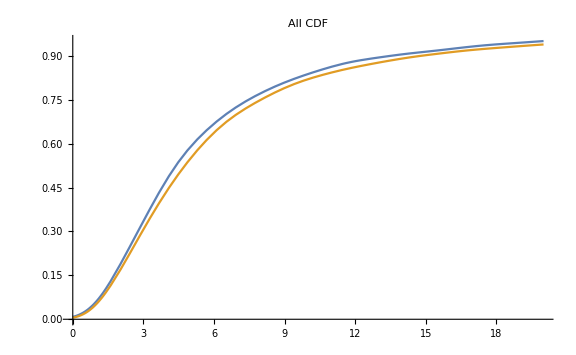

```mathematica
Table[Plot[{Evaluate[f[ABDist,x]],Evaluate[f[ANDist,x]]},{x,plotMin,plotMax},PlotLabel->("All "<>ToString[f]),ImageSize->Large],{f,{PDF,CDF}}]
```

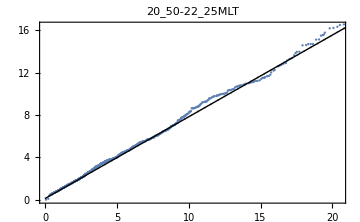
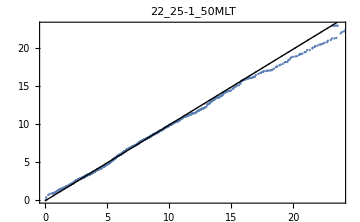
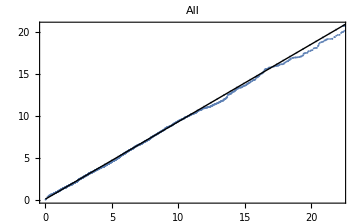

```mathematica
Table[QuantilePlot[dataz[[1]],dataz[[2]],PlotLabel->dataz[[3]],ImageSize->Medium],{dataz,{{EBData,ENData,earlyMLTStr},{LBData,LNData,lateMLTStr},{ABData,ANData,"All"}}}]
```

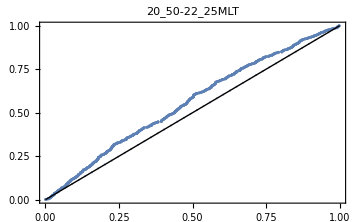
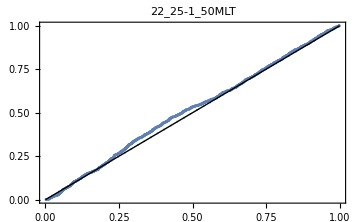
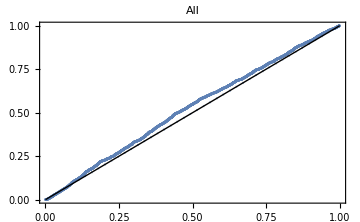

```mathematica
Table[ProbabilityPlot[dataz[[1]],dataz[[2]],PlotLabel->dataz[[3]],ImageSize->Medium],{dataz,{{EBData,ENData,earlyMLTStr},{LBData,LNData,lateMLTStr},{ABData,ANData,"All"}}}]
```

```mathematica
D1[list_]:=Quantile[list,1/10]
D3[list_]:=Quantile[list,3/10]
```

```mathematica
Q1[list_]:=Quantile[list,1/4]
Q3[list_]:=Quantile[list,3/4]
```

```mathematica
{{"","ABData","ANData"}}~Join~Table[{ToString@f,f[ABData+1.5],f[ANData+1.5]},{f,{D1,D3,Q1,Median,Q3,Mean}}]//TableForm
```

| ABData | ANData
D1 | 2.9691 | 3.03069
D3 | 4.27469 | 4.43066
Q1 | 3.9665 | 4.0924
Median | 5.55624 | 5.99447
Q3 | 8.92097 | 9.44788
Mean | 7.90818 | 8.45453

Essaye avec 20.5–22.25 MLT and 22.25–1.5 MLT divisions, use median

```mathematica
earlyMLTStr="20_50-22_25MLT";
lateMLTStr="22_25-1_50MLT";
```

```mathematica
dateStr="20180515-";
```

```mathematica
statType="ventile";
tile=10;
dstCutoff=-20;
```

```mathematica
EBData=loadKappaCSV["Early","Beam",dstCutoff,tile,statType,dateStr,earlyMLTStr->earlyMLTStr,lateMLTStr->lateMLTStr,subtract1point5->False];
ENData=loadKappaCSV["Early","NoBeam",dstCutoff,tile,statType,dateStr,earlyMLTStr->earlyMLTStr,lateMLTStr->lateMLTStr,subtract1point5->False];
LBData=loadKappaCSV["Late","Beam",dstCutoff,tile,statType,dateStr,earlyMLTStr->earlyMLTStr,lateMLTStr->lateMLTStr,subtract1point5->False];
LNData=loadKappaCSV["Late","NoBeam",dstCutoff,tile,statType,dateStr,earlyMLTStr->earlyMLTStr,lateMLTStr->lateMLTStr,subtract1point5->False];
ABData=loadKappaCSV["All","Beam",dstCutoff,tile,statType,dateStr,earlyMLTStr->earlyMLTStr,lateMLTStr->lateMLTStr,subtract1point5->False];
ANData=loadKappaCSV["All","NoBeam",dstCutoff,tile,statType,dateStr,earlyMLTStr->earlyMLTStr,lateMLTStr->lateMLTStr,subtract1point5->False];
```

```mathematica
EBDist=SmoothKernelDistribution[EBData];
ENDist=SmoothKernelDistribution[ENData];
LBDist=SmoothKernelDistribution[LBData];
LNDist=SmoothKernelDistribution[LNData];
ABDist=SmoothKernelDistribution[ABData];
ANDist=SmoothKernelDistribution[ANData];
```

```mathematica
plotMin=0;plotMax=20;
```

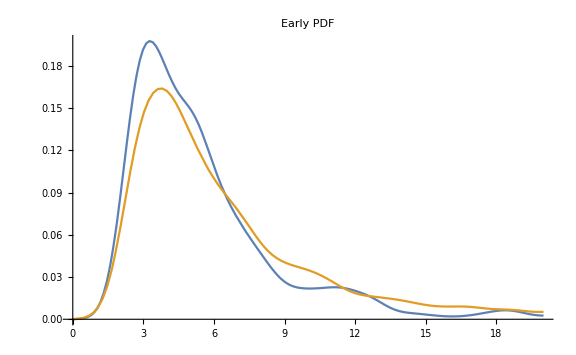
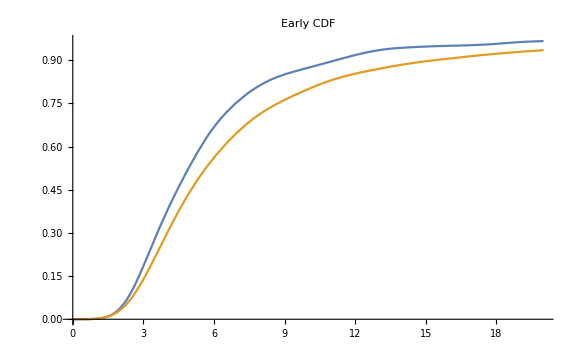

```mathematica
Table[Plot[{Evaluate[f[EBDist,x]],Evaluate[f[ENDist,x]]},{x,plotMin,plotMax},PlotLabel->("Early "<>ToString[f]),ImageSize->Large],{f,{PDF,CDF}}]
```

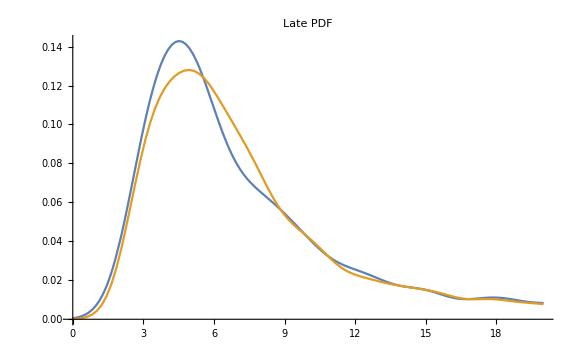
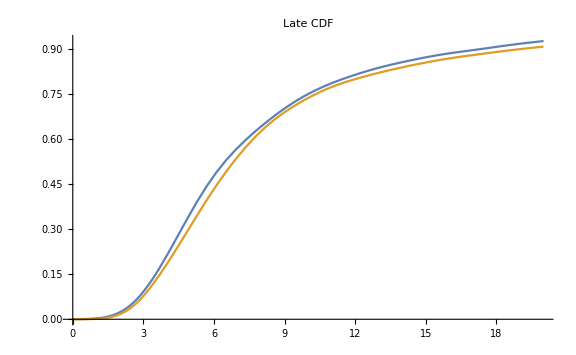

```mathematica
Table[Plot[{Evaluate[f[LBDist,x]],Evaluate[f[LNDist,x]]},{x,plotMin,plotMax},PlotLabel->("Late "<>ToString[f]),ImageSize->Large],{f,{PDF,CDF}}]
```

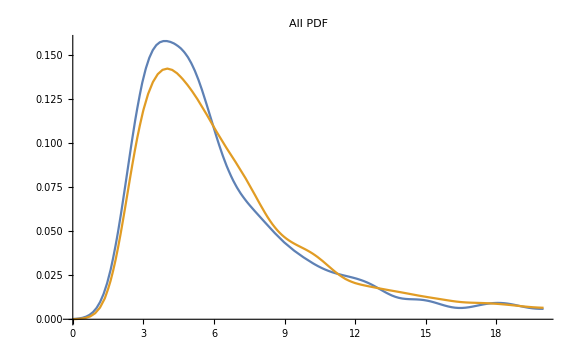
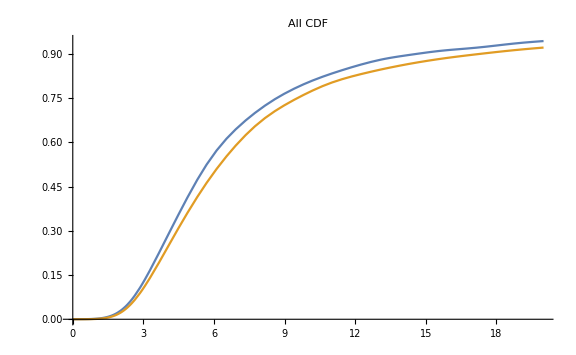

```mathematica
Table[Plot[{Evaluate[f[ABDist,x]],Evaluate[f[ANDist,x]]},{x,plotMin,plotMax},PlotLabel->("All "<>ToString[f]),ImageSize->Large],{f,{PDF,CDF}}]
```

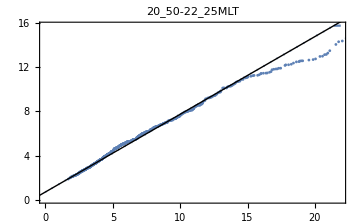
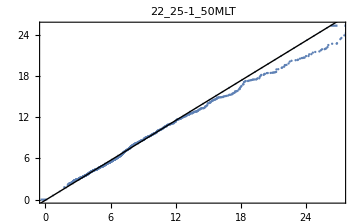
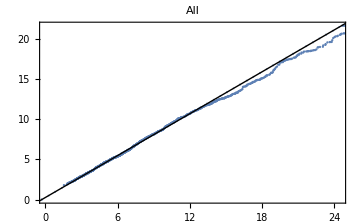

```mathematica
Table[QuantilePlot[dataz[[1]],dataz[[2]],PlotLabel->dataz[[3]],ImageSize->Medium],{dataz,{{EBData,ENData,earlyMLTStr},{LBData,LNData,lateMLTStr},{ABData,ANData,"All"}}}]
```

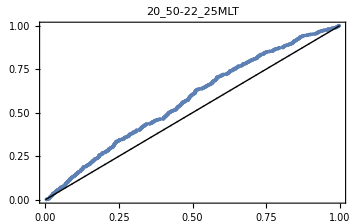
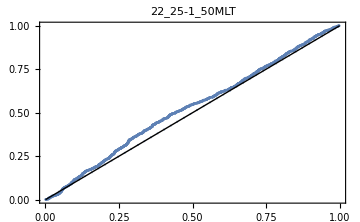
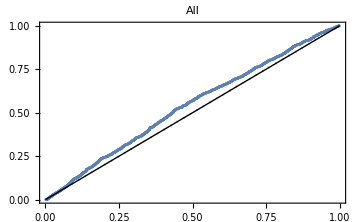

```mathematica
Table[ProbabilityPlot[dataz[[1]],dataz[[2]],PlotLabel->dataz[[3]],ImageSize->Medium],{dataz,{{EBData,ENData,earlyMLTStr},{LBData,LNData,lateMLTStr},{ABData,ANData,"All"}}}]
```

```mathematica
D1[list_]:=Quantile[list,1/10]
D3[list_]:=Quantile[list,3/10]
```

```mathematica
Q1[list_]:=Quantile[list,1/4]
Q3[list_]:=Quantile[list,3/4]
```

```mathematica
{{"","ABData","ANData"}}~Join~Table[{ToString@f,f[ABData],f[ANData]},{f,{D1,D3,Q1,Median,Q3,Mean}}]//TableForm
```

| ABData | ANData
D1 | 2.92489 | 3.02456
D3 | 4.13036 | 4.39104
Q1 | 3.80826 | 4.06747
Median | 5.40592 | 5.97819
Q3 | 8.55483 | 9.53024
Mean | 7.74867 | 8.70533

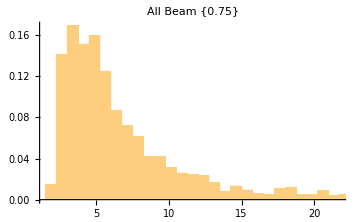
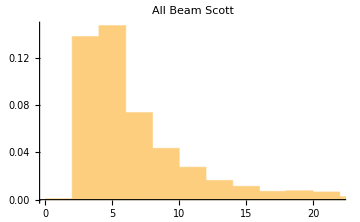
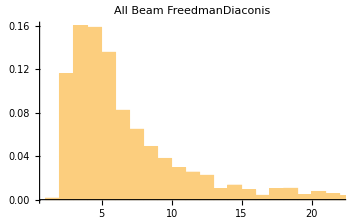
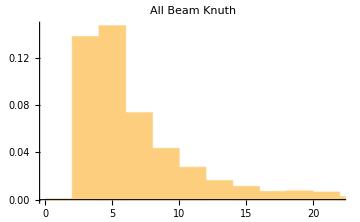
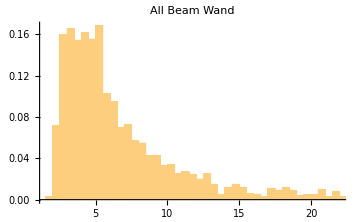

```mathematica
Table[plotLegends=If[ToString[bins]=="Wand",(ToString[#]& /@ strippedCandidates),None];
Histogram[ABData,bins,"PDF",PlotLabel->("All Beam "<>ToString[bins]),ImageSize->Medium],{bins,{{0.75},"Scott","FreedmanDiaconis","Knuth","Wand"}}]
```

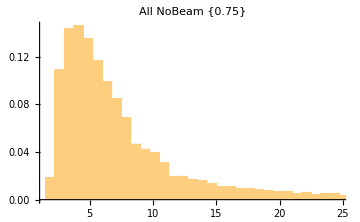
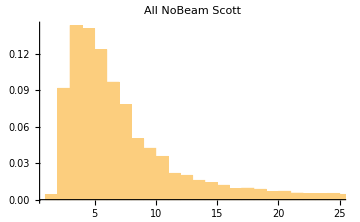
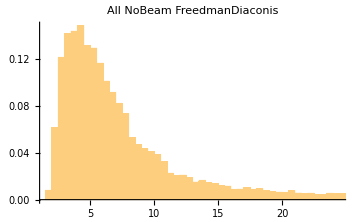
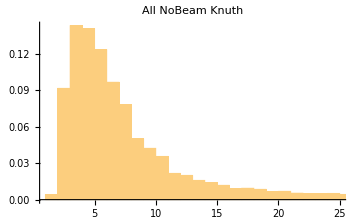
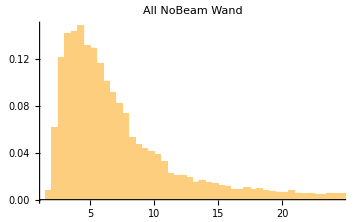

```mathematica
Table[plotLegends=If[ToString[bins]=="Wand",(ToString[#]& /@ strippedCandidates),None];
Histogram[ANData,bins,"PDF",PlotLabel->("All NoBeam "<>ToString[bins]),ImageSize->Medium],{bins,{{0.75},"Scott","FreedmanDiaconis","Knuth","Wand"}}]
```

Essaye avec 21-24 MLT divisions (IGNORE, GO TO journal__20180515__Fig3c.nb)

```mathematica
dateStr="20180516-";
```

```mathematica
allMLTStr="21-24MLT";
```

```mathematica
statType="ventile";
tile=10;
dstCutoff=-20;
```

```mathematica
If[ValueQ[allMLTStr],
Print["Using "<>allMLTStr<>" ..."];
ABData=loadKappaCSV["All","Beam",dstCutoff,tile,statType,dateStr,subtract1point5->False,allMLTStr->allMLTStr];
ANData=loadKappaCSV["All","NoBeam",dstCutoff,tile,statType,dateStr,subtract1point5->False,allMLTStr->allMLTStr];
,
ABData=loadKappaCSV["All","Beam",dstCutoff,tile,statType,dateStr,subtract1point5->False];
ANData=loadKappaCSV["All","NoBeam",dstCutoff,tile,statType,dateStr,subtract1point5->False];];
```

Using 21-24MLT ...

```mathematica
ABDist=SmoothKernelDistribution[ABData];
ANDist=SmoothKernelDistribution[ANData];
```

```mathematica
plotMin=0;plotMax=20;
```

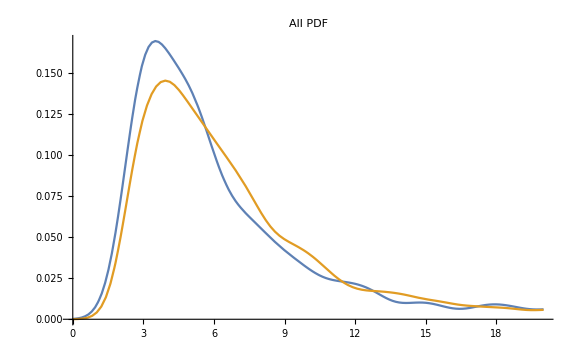
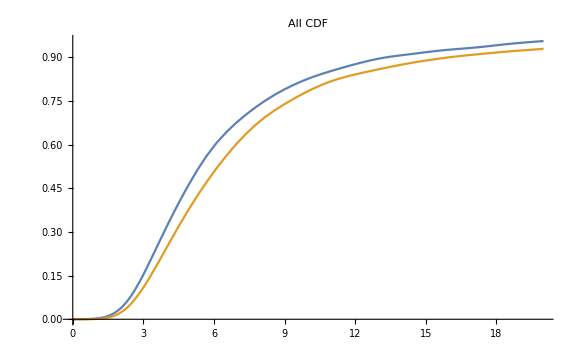

```mathematica
Table[Plot[{Evaluate[f[ABDist,x]],Evaluate[f[ANDist,x]]},{x,plotMin,plotMax},PlotLabel->("All "<>ToString[f]),ImageSize->Large],{f,{PDF,CDF}}]
```

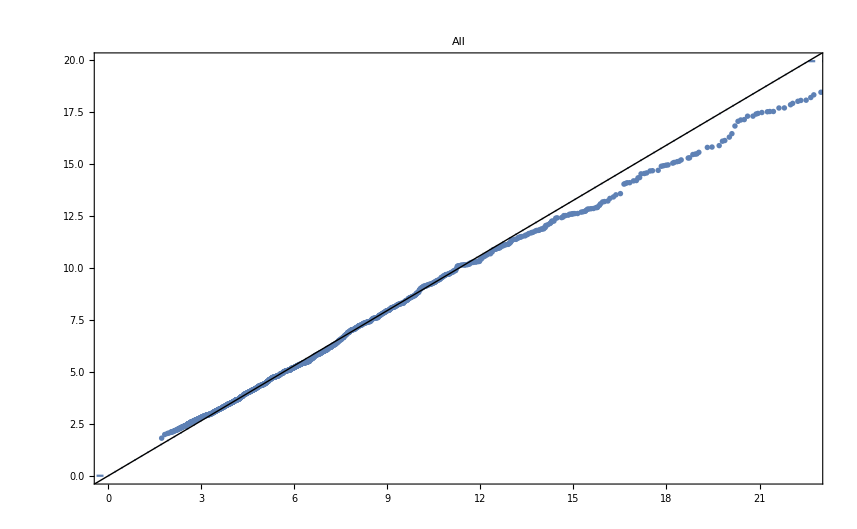

```mathematica
Table[QuantilePlot[dataz[[1]],dataz[[2]],PlotLabel->dataz[[3]],ImageSize->Medium],{dataz,{{ABData,ANData,"All"}}}]
```

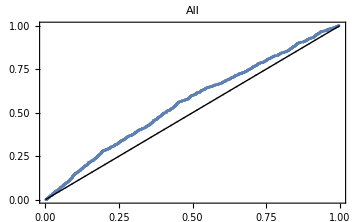

```mathematica
Table[ProbabilityPlot[dataz[[1]],dataz[[2]],PlotLabel->dataz[[3]],ImageSize->Medium],{dataz,{{ABData,ANData,"All"}}}]
```

```mathematica
D1[list_]:=Quantile[list,1/10]
D3[list_]:=Quantile[list,3/10]
```

```mathematica
Q1[list_]:=Quantile[list,1/4]
Q3[list_]:=Quantile[list,3/4]
```

```mathematica
{{"","ABData","ANData"}}~Join~Table[{ToString@f,f[ABData],f[ANData]},{f,{D1,D3,Q1,Median,Q3,Mean}}]//TableForm
```

| ABData | ANData
D1 | 2.79221 | 2.9897
D3 | 3.81774 | 4.32758
Q1 | 3.53628 | 4.0093
Median | 5.15926 | 5.91268
Q3 | 8.08713 | 9.16611
Mean | 7.20163 | 8.41226

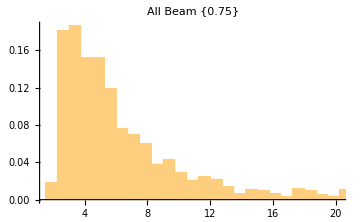
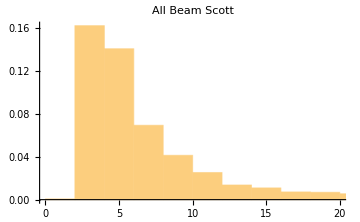
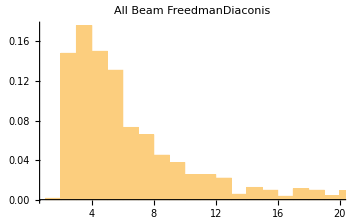
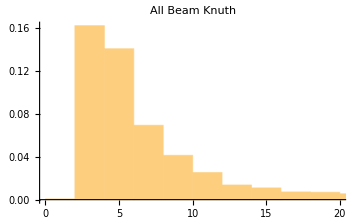
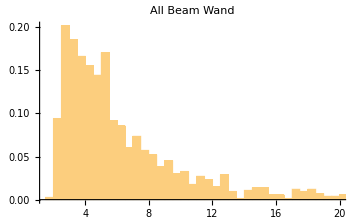

```mathematica
Table[plotLegends=If[ToString[bins]=="Wand",(ToString[#]& /@ strippedCandidates),None];
Histogram[ABData,bins,"PDF",PlotLabel->("All Beam "<>ToString[bins]),ImageSize->Medium],{bins,{{0.75},"Scott","FreedmanDiaconis","Knuth","Wand"}}]
```

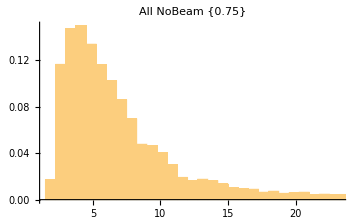
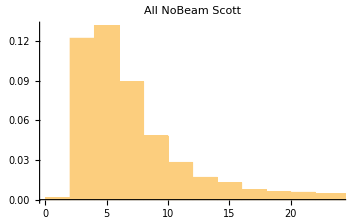
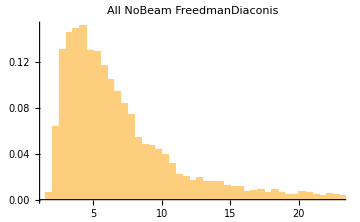
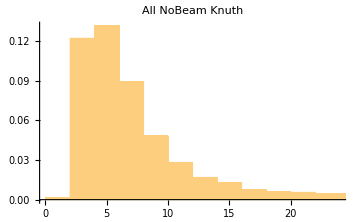
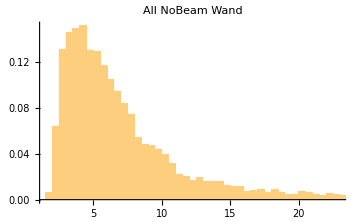

```mathematica
Table[plotLegends=If[ToString[bins]=="Wand",(ToString[#]& /@ strippedCandidates),None];
Histogram[ANData,bins,"PDF",PlotLabel->("All NoBeam "<>ToString[bins]),ImageSize->Medium],{bins,{{0.75},"Scott","FreedmanDiaconis","Knuth","Wand"}}]
```